# Inlämningsuppgift 2: Visualisering

IX1307 Problemlösning i Matematik, Inlämningsuppgift 2a, HT2019

Notebook-mall av Göran Andersson

## 1. Inledning

Denna uppgift går ut på att lösa ett antal matematiska problem med hjälp av Mathematica och skriva en kort rapport direkt i en egen Notebook. Rapporten skall, för varje uppgift, beskriva: problemet, figur, ange namn på variabler, lösningen till problemet inklusive resonemang och sedan diskutera resultatet.

Plagiering är inte tillåten, och källor måste anges när ni referera till annat material. Lämna in både en pdf-fil och notebook-filen i Canvas. Pdf-filen behövs för plagiatkontroll, då *.nb inte är accepeterad i URKUND.

## 2. Nyttiga funktioner i Mathematica

Lämpliga funktioner för att lösa uppgiften nedan, finns i datorövning 1 och 2 och föreläsningsanteckningar till momentet. Följande länkar kan vara lämpliga att studera:
"paclet:guide/ListManipulation"paclet:guide/ListManipulation
"paclet:FindFit"paclet:FindFit

## 3. Problem

Lös nedanstående problem. Problemets lösning och resultat skall innehålla visualisering där det är relevant.

### Analysera data

Nedan finns data för världens energikonsumtion i TWh/år för olika energislag och för världens totala energikonsumtion. Anpassa lämpliga modeller (exponentialmodel, linjär model, etc) till datat nedan så att du kan förutsäga världens framtida energiandvändning. Använd funktionen FindFit för att hitta lämpliga koefficienter till modellerna. Tips: Förskjut tidsskalan med t=t-1990 för att göra det enklare att hitta parametrarna i FindFit för icke-linjära anpassningar.

Svara på följande frågor:
1. Uppskatta världens energikonsumtion år 2050?
2. Uppskatta när olja som energikälla kan ersättas av förnybara energikällor?
3. Uppskatta om/när världens energikonsumtion är CO_2 fri?
4. Vilket förnybart energislag uppskattas vara viktigast år 2050?
5. Vad har val av modell för betydelse?
6.  Är ovanstående förutsägelser rimliga? Vilka felkällor finns?

#### Kol (TWh)

```mathematica
kol={{1990.,25845.88485},{1991.,25561.41954},{1992.,25478.81089},{1993.,25580.92144},{1994.,25729.64169},{1995.,25867.8533},{1996.,26516.28457},{1997.,26549.71899},{1998.,26351.79429},{1999.,26492.77461},{2000.,27403.94562},{2001.,27851.05371},{2002.,28936.6423},{2003.,31475.58334},{2004.,33656.31109},{2005.,36118.94545},{2006.,37979.81684},{2007.,40143.91171},{2008.,40712.5427},{2009.,40088.33994},{2010.,41932.74507},{2011.,43948.96889},{2012.,44129.62497},{2013.,44953.01385},{2014.,44916.83781},{2015.,43786.8458},{2016.,43101.23216},{2017.,43397.13549}};
```

#### Olja (TWh)

```mathematica
olja={{1990.,37736.94729},{1991.,37763.14824},{1992.,38422.53103},{1993.,38179.42324},{1994.,39021.80173},{1995.,39555.43054},{1996.,40480.1731},{1997.,41544.67299},{1998.,41768.48384},{1999.,42510.09274},{2000.,43038.62001},{2001.,43421.10755},{2002.,43796.55068},{2003.,44803.21017},{2004.,46503.96733},{2005.,47115.72728},{2006.,47732.19992},{2007.,48471.73162},{2008.,48250.64229},{2009.,47422.36853},{2010.,48949.72046},{2011.,49455.27172},{2012.,50065.86499},{2013.,50698.38455},{2014.,51109.97172},{2015.,52053.27008},{2016.,53001.86598},{2017.,53752.27638}};
```

#### Naturgas (TWh)

```mathematica
naturgas={{1990.,19486.64542},{1991.,19984.58677},{1992.,20076.92098},{1993.,20275.09431},{1994.,20405.36342},{1995.,21121.78818},{1996.,22143.41796},{1997.,22082.05319},{1998.,22485.93806},{1999.,23107.57158},{2000.,24019.89227},{2001.,24367.11133},{2002.,25108.12839},{2003.,25769.17552},{2004.,26752.16794},{2005.,27537.09099},{2006.,28347.57835},{2007.,29580.25097},{2008.,30321.37836},{2009.,29477.9263},{2010.,31759.12422},{2011.,32410.44868},{2012.,33270.53388},{2013.,33714.94785},{2014.,33986.84723},{2015.,34741.88349},{2016.,35741.82987},{2017.,36703.96587}};
```

#### Kärnkraft (TWh)

```mathematica
karnkraft={{1990.,2000.642591},{1991.,2096.356868},{1992.,2112.277946},{1993.,2185.016841},{1994.,2226.050783},{1995.,2322.592422},{1996.,2407.002623},{1997.,2390.480054},{1998.,2431.571247},{1999.,2524.546817},{2000.,2580.976669},{2001.,2653.821898},{2002.,2696.204132},{2003.,2641.599256},{2004.,2757.124087},{2005.,2769.046942},{2006.,2803.605088},{2007.,2746.479825},{2008.,2737.860822},{2009.,2699.245242},{2010.,2767.507814},{2011.,2651.771616},{2012.,2472.44864},{2013.,2491.705601},{2014.,2541.027341},{2015.,2575.664304},{2016.,2612.83283},{2017.,2635.561104}};
```

#### Bio-bränslen (TWh)

```mathematica
biobransle={{1990.,11111.11111},{1991.,11242.7549},{1992.,11375.95839},{1993.,11510.74008},{1994.,11647.11865},{1995.,11785.11302},{1996.,11924.74234},{1997.,12066.02598},{1998.,12208.98355},{1999.,12414.05573},{2000.,12500.},{2001.,12500.},{2002.,12470.},{2003.,12328.70237},{2004.,12159.75217},{2005.,12076.14729},{2006.,11993.11724},{2007.,11910.65806},{2008.,11828.76583},{2009.,11747.43666},{2010.,11666.66667},{2011.,11553.3766},{2012.,11441.18663},{2013.,11330.0861},{2014.,11220.06442},{2015.,11111.11111},{2016.,11003.2158},{2017.,10895.32049}};
```

#### Andra Förnybara Energikällor (TWh)

```mathematica
andrafornybara={{1990.,116.4628246},{1991.,121.4122701},{1992.,130.3448548},{1993.,134.7069628},{1994.,139.8004029},{1995.,145.5958811},{1996.,149.6884804},{1997.,160.9528063},{1998.,168.4548712},{1999.,177.1371664},{2000.,185.2722028},{2001.,191.0179267},{2002.,205.6996386},{2003.,217.2027959},{2004.,234.3682046},{2005.,254.3922875},{2006.,271.7633551},{2007.,294.2977297},{2008.,314.3656167},{2009.,338.2157334},{2010.,378.0383427},{2011.,397.4546676},{2012.,430.3624386},{2013.,463.9825019},{2014.,504.3899227},{2015.,538.2067786},{2016.,556.9861292},{2017.,586.1710901}};
```

#### Vattenkraft (TWh)

```mathematica
vatten={{1990.,2161.045291},{1991.,2213.110915},{1992.,2211.503167},{1993.,2344.266136},{1994.,2359.685227},{1995.,2488.983207},{1996.,2523.481143},{1997.,2569.633113},{1998.,2590.551798},{1999.,2608.338262},{2000.,2654.953445},{2001.,2586.668594},{2002.,2633.835653},{2003.,2629.430399},{2004.,2808.226932},{2005.,2918.064831},{2006.,3030.307944},{2007.,3079.79887},{2008.,3263.589026},{2009.,3253.601171},{2010.,3435.905581},{2011.,3503.227091},{2012.,3671.297583},{2013.,3797.954118},{2014.,3887.930335},{2015.,3891.408797},{2016.,4036.073668},{2017.,4059.868393}};
```

#### Vindkraft (TWh)

```mathematica
vind={{1990.,3.632470516},{1991.,4.086706675},{1992.,4.733212019},{1993.,5.697568819},{1994.,7.122929844},{1995.,8.261923444},{1996.,9.204610762},{1997.,12.01757667},{1998.,15.91490057},{1999.,21.21534431},{2000.,31.41996387},{2001.,38.39098735},{2002.,52.33180737},{2003.,62.91691456},{2004.,85.11605376},{2005.,104.0868359},{2006.,132.8592792},{2007.,170.6860872},{2008.,220.5696719},{2009.,275.9292658},{2010.,341.5652412},{2011.,436.8034429},{2012.,523.8148612},{2013.,645.7219776},{2014.,712.4070431},{2015.,831.8262454},{2016.,959.4687163},{2017.,1122.74585}};
```

#### Solenergi (TWh)

```mathematica
sol={{1990.,0.},{1991.,0.505223075},{1992.,0.468615413},{1993.,0.556737928},{1994.,0.60006443},{1995.,0.640874386},{1996.,0.705278679},{1997.,0.756655499},{1998.,0.880289501},{1999.,0.965823997},{2000.,1.177935576},{2001.,1.463956125},{2002.,1.831247734},{2003.,2.3293707},{2004.,3.054656084},{2005.,4.249617769},{2006.,5.818328387},{2007.,7.864870878},{2008.,12.72162081},{2009.,21.09259048},{2010.,33.82948514},{2011.,65.21188479},{2012.,100.9252749},{2013.,139.0442186},{2014.,197.6716635},{2015.,260.0058008},{2016.,328.1826964},{2017.,442.6183606}};
```

#### Världens total energikonsumtion (TWh)

```mathematica
totalt={{1990.,98462.371847116},{1991.,98987.38143285},{1992.,99813.54908523199},{1993.,100216.423316547},{1994.,101537.18489717401},{1995.,103296.25934793001},{1996.,106154.70010584098},{1997.,107376.31135546902},{1998.,108022.57284627101},{1999.,109856.69807370701},{2000.,112416.258116246},{2001.,113610.635952175},{2002.,115901.223848704},{2003.,119930.15013616001},{2004.,124960.08846344402},{2005.,128897.75152416898},{2006.,132297.06634468702},{2007.,136405.679742778},{2008.,137662.43593741},{2009.,135324.15543267998},{2010.,141265.10288404},{2011.,144422.53459229},{2012.,146106.05926769998},{2013.,148234.8407671},{2014.,149077.14748530003},{2015.,149790.2224058},{2016.,151341.68784990002},{2017.,153595.6630277}};
```

## Uppgift 1 - Uppskattning av världens energikonsumtion år 2050

## Uppgift 2 - Uppskattning av när olja ersätts av förnybara energikällor

### Problemformulering

```mathematica
Quit[]
```

```mathematica
?Total
```

```mathematica
?Table
```

```mathematica
{#[[1,1]],Total[#[[All,2]]]}&/@GatherBy[Flatten[,1],First]
```

### Lösning

(1) Det första som görs för att lösa uppgiften är att identifera och lista de energikällor som anses vara förnybara enligt energimyndighetens definition (https://www.energimyndigheten.se/fornybart/)

```mathematica
Förnybarenergi=Table [{totalt⟦i,1⟧, biobransle⟦i,2⟧+andrafornybara⟦i,2⟧+vatten⟦i,2⟧+vind⟦i,2⟧+sol⟦i,2⟧},{i,1,Length[totalt]}]
```

{{1990.,13392.3},{1991.,13581.9},{1992.,13723.},{1993.,13996.},{1994.,14154.3},{1995.,14428.6},{1996.,14607.8},{1997.,14809.4},{1998.,14984.8},{1999.,15221.7},{2000.,15372.8},{2001.,15317.5},{2002.,15363.7},{2003.,15240.6},{2004.,15290.5},{2005.,15356.9},{2006.,15433.9},{2007.,15463.3},{2008.,15640.},{2009.,15636.3},{2010.,15856.},{2011.,15956.1},{2012.,16167.6},{2013.,16376.8},{2014.,16522.5},{2015.,16632.6},{2016.,16883.9},{2017.,17106.7}}

```mathematica
TableForm[Förnybarenergi,TableHeadings-> {None,{"År","TWh"}}]
```

År | TWh
1990. | 13392.3
1991. | 13581.9
1992. | 13723.
1993. | 13996.
1994. | 14154.3
1995. | 14428.6
1996. | 14607.8
1997. | 14809.4
1998. | 14984.8
1999. | 15221.7
2000. | 15372.8
2001. | 15317.5
2002. | 15363.7
2003. | 15240.6
2004. | 15290.5
2005. | 15356.9
2006. | 15433.9
2007. | 15463.3
2008. | 15640.
2009. | 15636.3
2010. | 15856.
2011. | 15956.1
2012. | 16167.6
2013. | 16376.8
2014. | 16522.5
2015. | 16632.6
2016. | 16883.9
2017. | 17106.7

(2) Sedan sammanställs data för energiförbrukningen av olja

```mathematica
tblolja=Table[olja]
```

{{1990.,37736.9},{1991.,37763.1},{1992.,38422.5},{1993.,38179.4},{1994.,39021.8},{1995.,39555.4},{1996.,40480.2},{1997.,41544.7},{1998.,41768.5},{1999.,42510.1},{2000.,43038.6},{2001.,43421.1},{2002.,43796.6},{2003.,44803.2},{2004.,46504.},{2005.,47115.7},{2006.,47732.2},{2007.,48471.7},{2008.,48250.6},{2009.,47422.4},{2010.,48949.7},{2011.,49455.3},{2012.,50065.9},{2013.,50698.4},{2014.,51110.},{2015.,52053.3},{2016.,53001.9},{2017.,53752.3}}

```mathematica
TableForm[tblolja,TableHeadings-> {None,{"År","TWh"}}]
```

År | TWh
1990. | 37736.9
1991. | 37763.1
1992. | 38422.5
1993. | 38179.4
1994. | 39021.8
1995. | 39555.4
1996. | 40480.2
1997. | 41544.7
1998. | 41768.5
1999. | 42510.1
2000. | 43038.6
2001. | 43421.1
2002. | 43796.6
2003. | 44803.2
2004. | 46504.
2005. | 47115.7
2006. | 47732.2
2007. | 48471.7
2008. | 48250.6
2009. | 47422.4
2010. | 48949.7
2011. | 49455.3
2012. | 50065.9
2013. | 50698.4
2014. | 51110.
2015. | 52053.3
2016. | 53001.9
2017. | 53752.3

(3) Datapunkterna visualiseras sedan med kommandot “ListPlot”

Set::write: Tag Dot in oil.vs.förnyb is Protected.

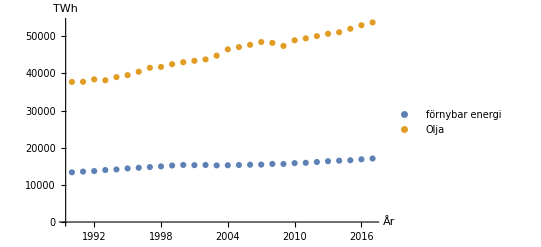

```mathematica
oil.vs.förnyb=ListPlot[{Förnybarenergi,tblolja}, PlotLegends->{"förnybar energi","Olja"},AxesLabel-> {"År","TWh"}]
```

(4) Nästa steg är att försöka hitta den modell som bäst passar utvecklingen. En logaritmisk, en polynomfunktion och en rätlinjig tas fram.

```mathematica
Fit[Förnybarenergi,{1,x,x^2},x]
```

-3.76824×10^6+3661.88 x-0.885143 x^2

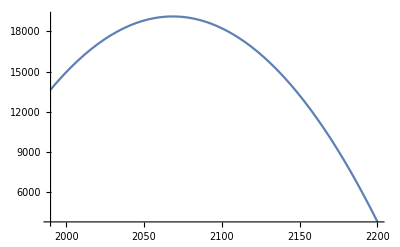

```mathematica
Plot[-3.768238607878448*^6+3661.8804058958776 x-0.8851434960813085 x^2,{x,1990,2200}]
```

```mathematica
Fit[tblolja,{1,x,x^2},x]
```

-4.25883×10^6+3690.43 x-0.769717 x^2

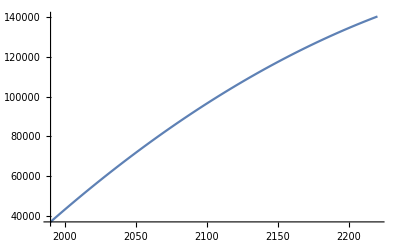

```mathematica
Plot[-4.258833510398464*^6+3690.427767392037 x-0.7697165533408139 x^2,{x,1990,2220}]
```

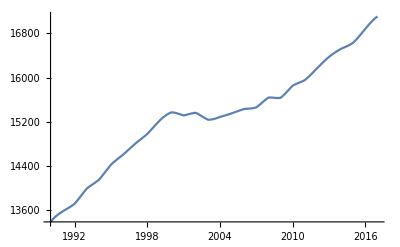

```mathematica
Plot[f[x],{x,1990,2017}]
```

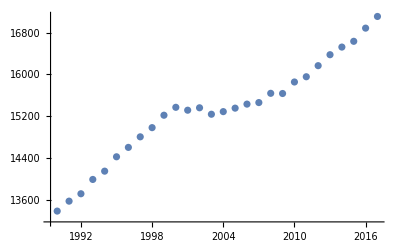

```mathematica
Plott1=ListPlot[Förnybarenergi]
```

(2) Sedan görs en kvadratisk modell en linjär.

```mathematica
f[t_]=LinearModelFit[Förnybarenergi,{t^2,t},t]
```

FittedModel[-3.76824×10^6+3661.88 t-0.885143 t^2]

```mathematica
p1=Plot[-3.7682386078789392*10^6+3661.880405896371 t-0.8851434960814328 t^2,{t,1990,2200}]
```

-Graphics-

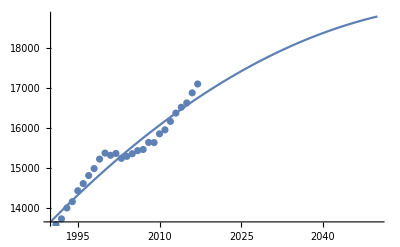

```mathematica
Show[p1,Plott1]
```

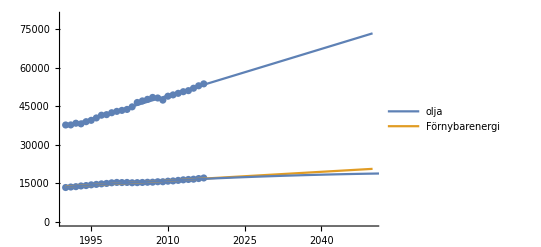

```mathematica
Show[Plott1,ListPlotOlja,ppp,p1, PlotRange-> {{1990,2220},{0,80000}},AxesOrigin-> Automatic]
```

```mathematica
Table[olja]
```

{{1990.,37736.9},{1991.,37763.1},{1992.,38422.5},{1993.,38179.4},{1994.,39021.8},{1995.,39555.4},{1996.,40480.2},{1997.,41544.7},{1998.,41768.5},{1999.,42510.1},{2000.,43038.6},{2001.,43421.1},{2002.,43796.6},{2003.,44803.2},{2004.,46504.},{2005.,47115.7},{2006.,47732.2},{2007.,48471.7},{2008.,48250.6},{2009.,47422.4},{2010.,48949.7},{2011.,49455.3},{2012.,50065.9},{2013.,50698.4},{2014.,51110.},{2015.,52053.3},{2016.,53001.9},{2017.,53752.3}}

```mathematica
TableForm[%37,TableHeadings-> {None,{"År","TWh"}}]
```

År | TWh
1990. | 37736.9
1991. | 37763.1
1992. | 38422.5
1993. | 38179.4
1994. | 39021.8
1995. | 39555.4
1996. | 40480.2
1997. | 41544.7
1998. | 41768.5
1999. | 42510.1
2000. | 43038.6
2001. | 43421.1
2002. | 43796.6
2003. | 44803.2
2004. | 46504.
2005. | 47115.7
2006. | 47732.2
2007. | 48471.7
2008. | 48250.6
2009. | 47422.4
2010. | 48949.7
2011. | 49455.3
2012. | 50065.9
2013. | 50698.4
2014. | 51110.
2015. | 52053.3
2016. | 53001.9
2017. | 53752.3

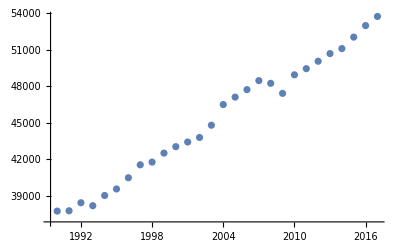

```mathematica
ListPlotOlja=ListPlot[olja]
```

```mathematica
{etot,ftot}=
{et,ft}/.FindFit [olja,{et(t-1990)+ ft},{et ,ft},t]
```

{606.174,37053.3}

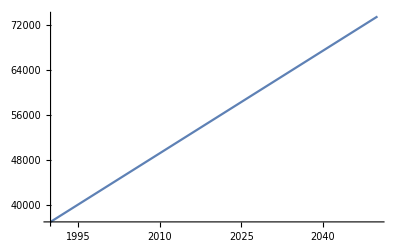

```mathematica
ptot2=Plot[etot(t-1990)+ ftot ,{t,1990,2050}]
```

```mathematica
{ctot,dtot}=
{ct,dt}/.FindFit [Förnybarenergi,{ct(t-1990)+ dt},{ct ,dt},t]
```

{115.11,13750.2}

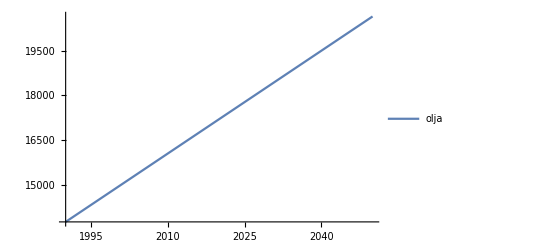

```mathematica
ptot3=Plot[ ctot * (t-1990)+ dtot,{t,1990,2050},PlotLegends->{"olja"}]
```

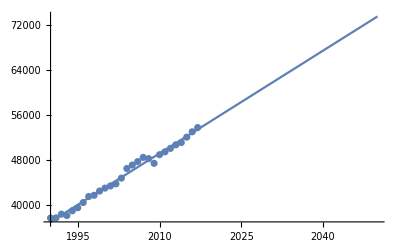

```mathematica
Show[ptot2,ListPlotOlja]
```

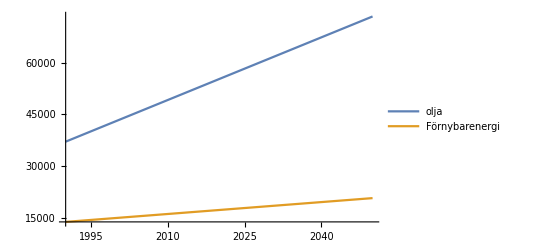

```mathematica
ppp=Plot[{etot(t-1990)+ ftot ,ctot * (t-1990)+ dtot},{t,1990,2050},AxesOrigin-> Automatic,PlotLegends->{"olja","Förnybarenergi"}]
```

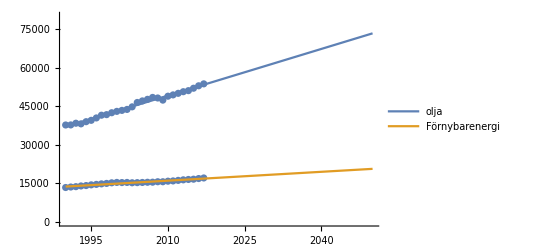

```mathematica
Show[Plott1,ListPlotOlja,ppp, PlotRange-> {{1990,2050},{0,80000}},AxesOrigin-> Automatic]
```

```mathematica
Solve[etot(t-1990)+ ftot==ctot * (t-1990)+ dtot]
```

{{t→1942.55}}

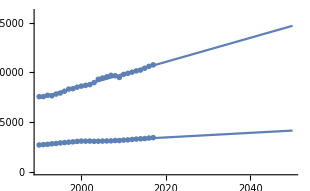
```mathematica
-Graphics-ListLinePlot[Table[f,{f,{Log[x],x^(1/2)}},{x,0,10,0.1}],DataRange->{0,10},PlotLegends->Placed[{"log(x)","\!\(\*SuperscriptBox[\(x\), \(1/2\)]\)"},Above]]
```

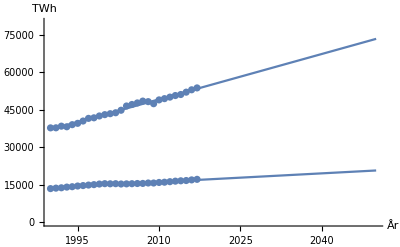

```mathematica
Show[%62,AxesLabel->{HoldForm[År],HoldForm[TWh]},PlotLegends->{"Olja","Förnybarenergi"}]
```